```mathematica
$HistoryLength=10;
mb=9.27*(10^-21);
Mf=10*mb;
Md=5*mb;
l=(10^5)/mb;
Kf0=2.55*(10^-16);
Kd0=2.55*(10^-16);
Cnorm = 10^14;
h0 = 2*10^5;
x0 = 0.35;
len0=31;
Hmin = -10^6;
Hmax = 10^6;
Xmin = 0.1;
Xmax = 1;
```

```mathematica
Heff[θ_, h_] := Sqrt[h^2 + (l*Md)^2 - 2*l*h*Md*Cos[θ]]
cosf[θ_, h_]:=(h-l*Md*Cos[θ])/Heff[θ,h] 
Energy[θ_, x_, h_, Kd_:Kd0, Kf_:Kf0] := (-x*Mf*Heff[θ,h]-Md*h*(1-x)*Cos[θ]-Kd*(1-x)*Cos[θ]^2-Kf*x*cosf[θ,h]^2)*Cnorm
dEnergy[θ_, x_, h_, Kd_:Kd0, Kf_:Kf0]:=Derivative[1,0,0,0,0][Energy][θ, x, h, Kd, Kf]
ddEnergy[θ_, x_, h_, Kd_:Kd0, Kf_:Kf0]:=Derivative[2,0,0,0,0][Energy][θ, x, h, Kd, Kf]
```

```mathematica
len=len0;
Hist[x0_, Kd_:Kd0 * 5 , Kf_:Kf0 * 5]:= Module[{H, Θ1, Θ2, td},
H  = Range[ Hmin, Hmax , 2*Hmax/len];
Θ1 = Table[Cos[θ]/.Solve[dEnergy[θ, x0, h, Kd, Kf] == 0&& ddEnergy[θ, x0, h, Kd, Kf]≥ 0 && -π<θ≤π, θ][[1]],
{h, Hmin  ,Hmax,  2*Hmax/len}];
Θ2 = Table[Cos[θ]/.Solve[dEnergy[θ, x0, h,Kd, Kf]  == 0&& ddEnergy[θ, x0, h, Kd, Kf]≥ 0 && -π<θ≤π, θ][[-1]],
{h, Hmin, Hmax , 2*Hmax/len}];
td= TemporalData[{Θ1, Θ2}, {H}];
tickSpecification = Table[{i,N[i * 10^-6]}, {i, -10^6, 10^6, 250000}];
ListLinePlot[td, PlotLabel->Style[StringForm["Stoichiometric coefficient x = ``",x0], Bold], PlotMarkers->Automatic,Ticks->{tickSpecification, Automatic}, PlotLegends->{"θ_1", "θ_2"}, AxesLabel->{"H, 10^6", "cos(θ)"}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

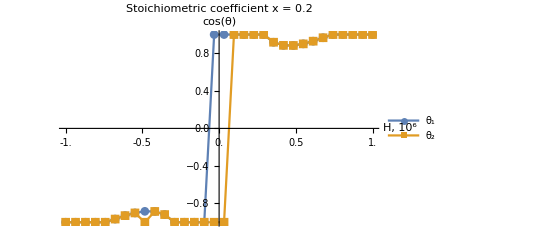
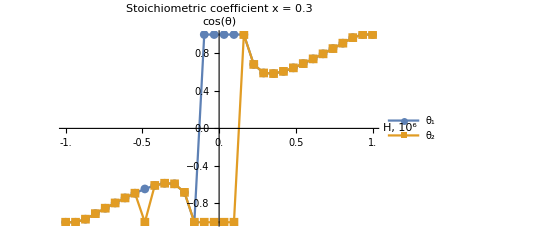
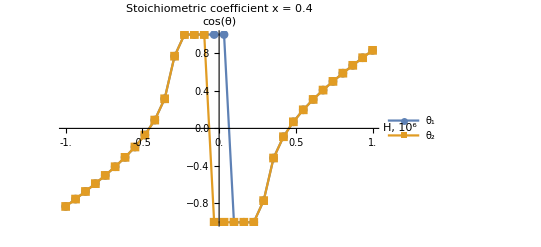
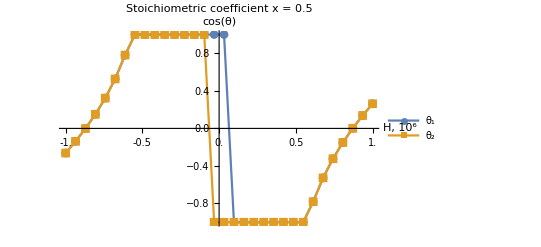

```mathematica
Map[Hist, Range[0.2, 0.5, 0.1]]
```

```mathematica
Manipulate[Plot[Energy[θ, x, h], {θ,-2π,2π}], {x, 0, 1}, {h,-10^6,10^6}]
```

```mathematica
TickTable[len_] := Table[{i, N[i/len]}, {i,0, len, 6}]
VectorMd[len_,Kd_:Kd0, Kf_:Kf0]:= ListVectorPlot[Table[{Sin[θ]/.Solve[dEnergy[θ, x, h, Kd, Kf] == 0&& ddEnergy[θ, x, h, Kd, Kf]≥ 0 && -π<θ≤π, θ][[-1]],
Cos[θ]/.Solve[dEnergy[θ, x, h, Kd, Kf] ==0&& ddEnergy[θ, x, h, Kd, Kf]≥ 0 && -π<θ≤π, θ][[-1]]},
{x,0.1, 1, (Xmax-Xmin)/len},	
{h, 1, Hmax ,Hmax/len}], VectorPoints->len, FrameTicks ->{TickTable[len], TickTable[len]}, FrameLabel -> {"x", "H, 10^6"},PlotLabel->Style[StringForm["K_d = `1`erg,   K_f = `2`erg", Kd, Kf ],Bold]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

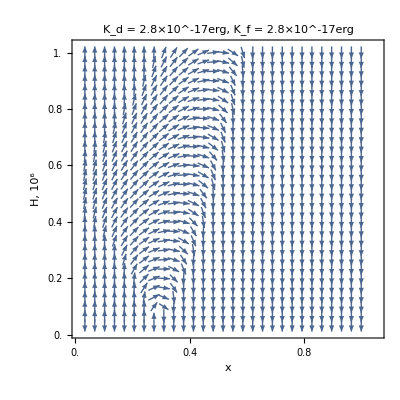
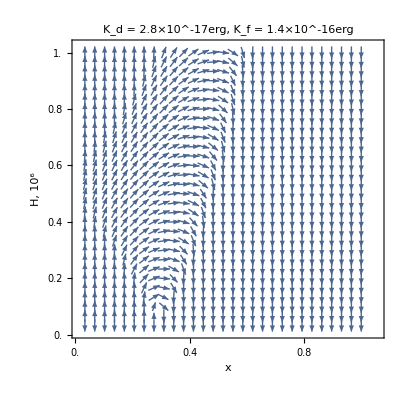
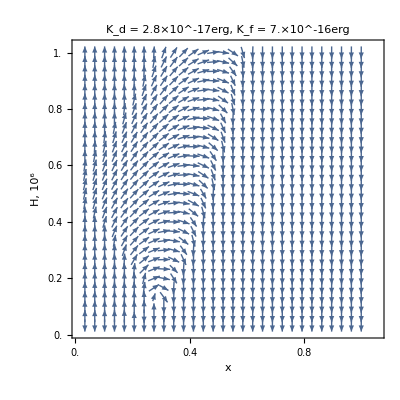
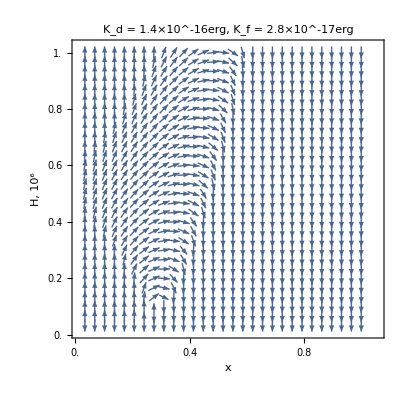
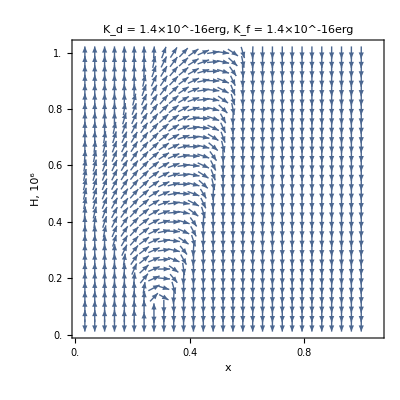
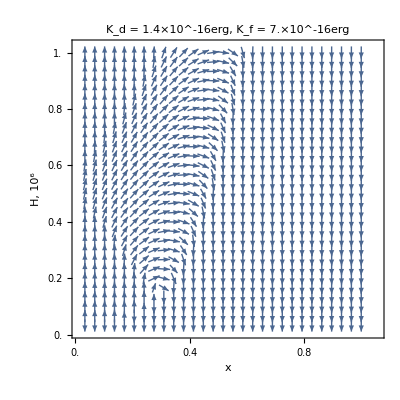
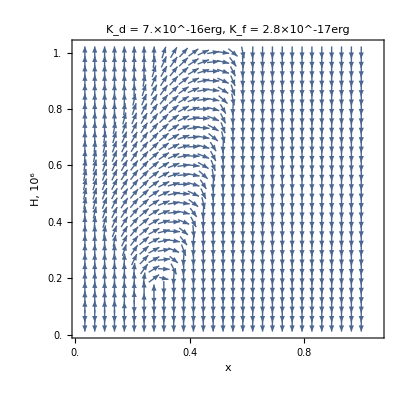
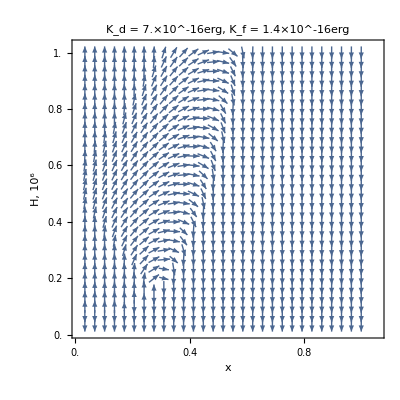

```mathematica
K = Flatten[Table[{Kd0 * 5^i, Kf0 * 5^j}, {i, -1, 1, 1}, {j, -1, 1, 1}], 1];
VectorMd[30, #1, #2]& @@@K
```

```mathematica
ArrayReshape[%, {3,3}]
```

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
xmin = 0.33;
xmax = 0.3425;
xstep = 0.00025;
xlen = Round[(xmax-xmin)/xstep]
hmin = 0.8 * 10^5;
hmax = 1.05 * 10^5;
hstep = 0.005*10^5;
hlen = Round[(hmax-hmin)/hstep]
ticksX = Transpose[
{ Table[i, { i,0, xlen, 5}],
Table[xmin + i*xstep ,{i, 0, xlen, 10}]}
];
ticksH = Transpose[
{ Table[i, { i,0, hlen, 5}],
Table[hmin + i*hstep ,{i, 0, hlen, 10}]}
];
```

50

50

```mathematica
VectorMf[Kd_:Kd0, Kf_:Kf0]:= 
ListVectorPlot[
Table[
{Sqrt[1-(cosf[θ, h])^2]/.Solve[dEnergy[θ, x, h, Kd, Kf] == 0&& ddEnergy[θ, x, h, Kd, Kf]≥ 0 && -π<θ≤π, θ][[-1]],
cosf[θ, h]/.Solve[dEnergy[θ, x, h, Kd, Kf] ==0&& ddEnergy[θ, x, h, Kd, Kf]≥ 0 && -π<θ≤π, θ][[-1]]},
{x,xmin, xmax, xstep},
{h, hmin, hmax ,hstep}
],
VectorPoints->{xlen,hlen},
FrameTicks->{{ticksH, None},{ticksX, None}}
]
```

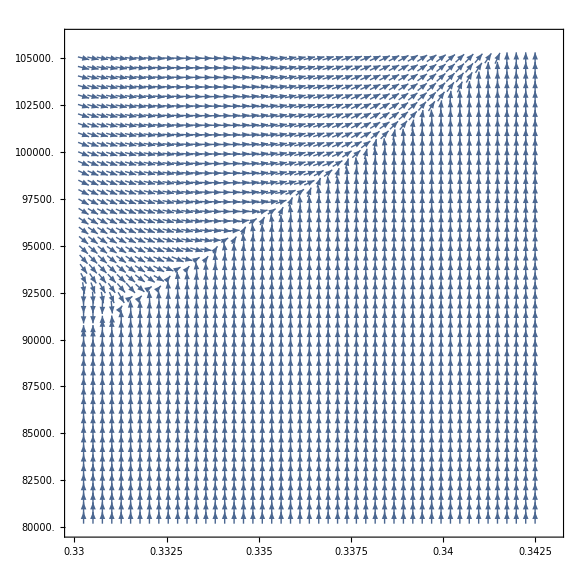

```mathematica
VectorMf[]
```

```mathematica
spinsPlot = %436;
```

%436

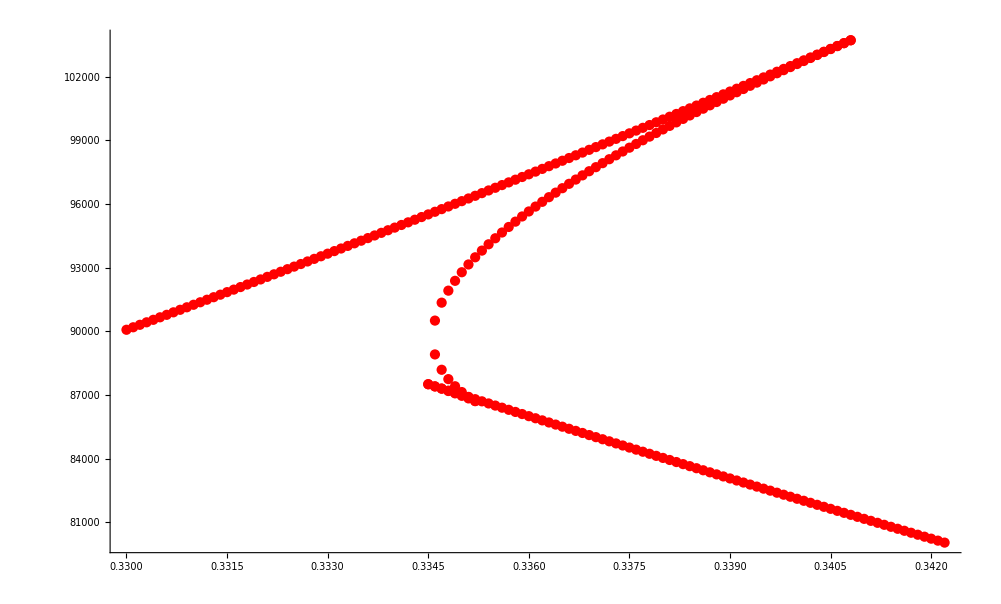

```mathematica
Points = Import["/home/koritskiy/rqc/ferrimagnet/crit_fields_0.33-0.35.dat"];
buckling = ListPlot[Points, PlotStyle -> Red, DataRange->{{0.33, 0.3425},{80000, 105000}}]
```

```mathematica
Export["transparent.png",buckling,Background->None, ImageSize->{3000, 3000}]
```

transparent.png

```mathematica
.13
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["transparent.png"]]]
```

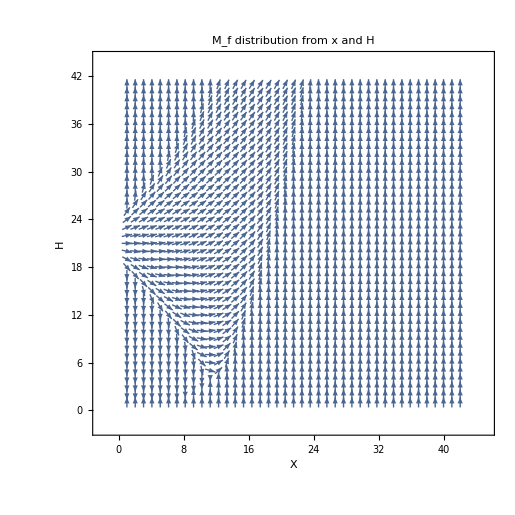

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.